```mathematica
Using this notebook replace the data with your data.  Plot and fit the data with the function "Fit[data, {1,Sqrt[x]},x]".  Then using the "Show" command show the fit and data on one plot.  Make this plot publication ready by adding axes labels and units, etc.

each cells is executed by pressing SHIFT+ENTER
```

```mathematica
data={{2.,5.9},{2.4,5.52},{2.7,5.96},{3.1,6.4},{3.3,7.01},{3.7,7.23},{4.12,7.77},{4.9,8.2},{5.65,9.0},{5.72,9.2},{6.86,9.96}}
```

{{2.,5.9},{2.4,5.52},{2.7,5.96},{3.1,6.4},{3.3,7.01},{3.7,7.23},{4.12,7.77},{4.9,8.2},{5.65,9.},{5.72,9.2},{6.86,9.96}}

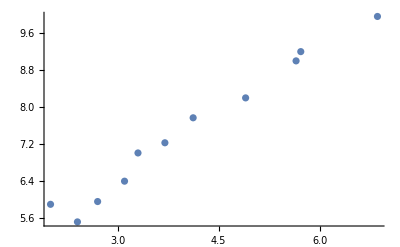

```mathematica
plot1=ListPlot@data
```

```mathematica
fit1=Fit[data, {1,Sqrt[x]},x]
```

-0.0365173+3.79748 √x

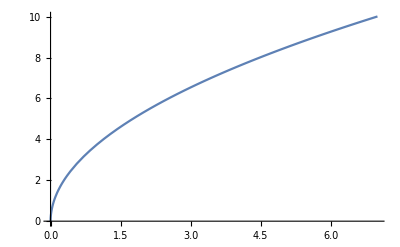

```mathematica
plot2=Plot[fit1,{x,0,7}]
```

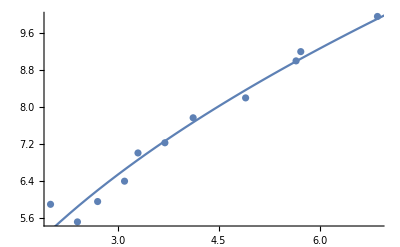

```mathematica
Show[plot1, plot2]
```

```mathematica
Now Linearize the data name it "datalinear" and plot T^2 vs m.  Then fit the data using "Fit[datalinear,{1,x},x]"  Display the fit and the data together with in a publication ready graph.
```

```mathematica
data2=Import["D:\\121EngineeringScience\\121CloudData\\data.csv","CSV"];
column1=data2[[All,1]]
column2=data2[[All,2]]
```

{2.,2.2,2.5,3.,3.4,3.7,4.1,4.8,5.6,5.7,6.8}

{5.4,5.52,5.96,6.52,6.98,7.23,7.63,8.27,8.96,9.,9.86}

```mathematica
data3=Riffle[column1,column2]~Partition~2
```

{{2.,5.4},{2.2,5.52},{2.5,5.96},{3.,6.52},{3.4,6.98},{3.7,7.23},{4.1,7.63},{4.8,8.27},{5.6,8.96},{5.7,9.},{6.8,9.86}}

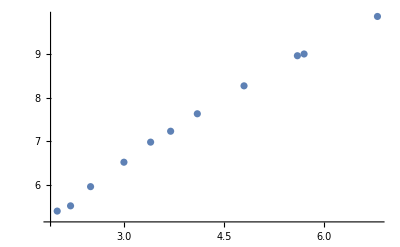

```mathematica
plot3=ListPlot@data3
```

-0.03581+3.79134 √x

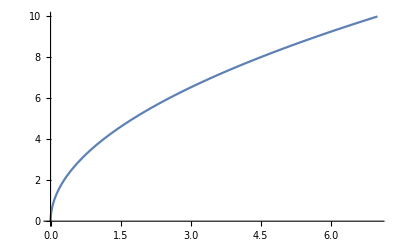

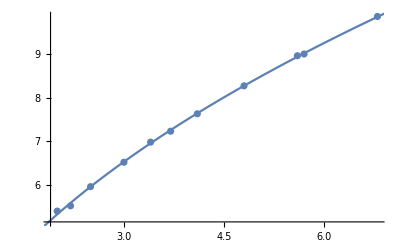

```mathematica
fit2=Fit[data3, {1,Sqrt[x]},x]
plot4=Plot[fit2,{x,0,7}]
Show[plot3, plot4]
```

```mathematica
sqList[column1_]:=column1^2
column3=sqList[column2]
```

{29.16,30.4704,35.5216,42.5104,48.7204,52.2729,58.2169,68.3929,80.2816,81.,97.2196}

```mathematica
data4=Riffle[column1,column3]~Partition~2
```

{{2.,29.16},{2.2,30.4704},{2.5,35.5216},{3.,42.5104},{3.4,48.7204},{3.7,52.2729},{4.1,58.2169},{4.8,68.3929},{5.6,80.2816},{5.7,81.},{6.8,97.2196}}

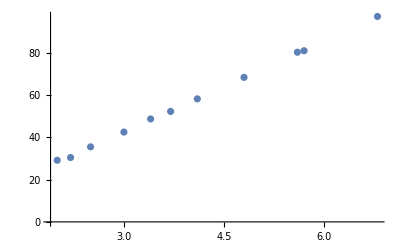

-0.335903+14.3256 x

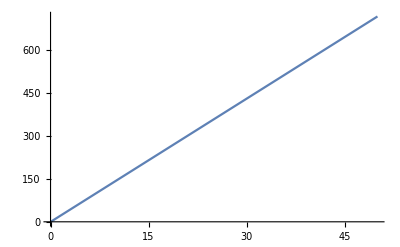

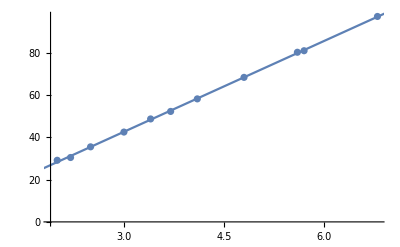

```mathematica
plot5=ListPlot@data4
fit3=Fit[data4, {1,x},x]
plot6=Plot[fit3,{x,0,50}]
Show[plot5, plot6]
```